# 0) Preliminaries

```mathematica
plotFun[fun_,lims_,epilog_,label_,legs_:None]:=Framed@Plot[fun,{x,lims[[1,1]],lims[[1,2]]},PlotRange->{Full,{lims[[2,1]],lims[[2,2]]}},Epilog->epilog,PlotLegends->legs,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"x","y"},BaseStyle->{FontSize->20}]
```

```mathematica
discPlotFun[fun_,range_,lims_,epilog_,label_]:=Framed@DiscretePlot[fun,{n,range[[1]],range[[2]]},PlotRange->lims,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"M","y"},BaseStyle->{FontSize->20}]
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
If[ilimpos===Automatic,ilimpos={22,limit+05}];
funplot=DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0}(*{(*maxran-20*)20,limit+.05}*),{(*maxran-25*)(*15*)ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos(*{(*maxran-20*)22,limit+.05}*),Left]},{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]},Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" }
]
]*)
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,upreg_:True,lowreg_:True,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
If[ilimpos===Automatic,ilimpos={22,limit+05}];
funplot=DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{
(*limit line and label*)
{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0},{ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos,Left]},

(*lower region*)
If[upreg,{{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]}},{}],

(*upper region*)
If[lowreg,{{Thick,Orange,Line[{{0,limit+ϵ},{maxran,limit+ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit+ϵ}}],Text[Style["ϵ",20],{4,limit+ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit+ϵ},{maxran,limit}]}},{}],

(*moving n0*)
Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]
}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" }
]
]*)
```

```mathematica
ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,upreg_:True,lowreg_:True,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" },
{{funplot,DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}]},{0,1},ControlType->None},
{{ilimpos,If[limpos===Automatic,{22,limit+05},limpos]},ControlType->None},
SaveDefinitions->True,Initialization:>{epsplot[ϵ_]:=Graphics[{
(*limit line and label*)
{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0},{ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos,Left]},

(*lower region*)
If[upreg,{{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]}},{}],

(*upper region*)
If[lowreg,{{Thick,Orange,Line[{{0,limit+ϵ},{maxran,limit+ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit+ϵ}}],Text[Style["ϵ",20],{4,limit+ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit+ϵ},{maxran,limit}]}},{}],

(*moving n0*)
Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]
}]}
]
]
```

# 1) Sinc

a) lim_(x→0) (sin(x))/x=1 ?

b) stetige Fortsetzung bei x=0 ?

c) Graph

#### Useful formulas

Sin vs. Exp

sin(x)=1/(2ⅈ)ⅇ^(-ⅈ x)(ⅇ^(2 ⅈ x)-1)

Restgliedabschätzung für die komplexe Exponentialfunktion

exp(x)=∑_(n=0)^N x^n/(n!)+R_(N+1)(x),

Abs[R_(N+1)(x)]≤2 Abs[x]^(N+1)/((N+1)!),  Abs[x]≤N/2+1

Limit of a function

f: D→ℝ;  D⊂ℝ;  x_0∈ℝ   Häufungspunkt

lim_(x→x_0) f(x)=y_0

∀(a_n)⊂D,a_n≠x_0, lim_(n→∞) a_n=x_0:  lim_(n→∞) f(a_n)=y_0

## Solution

## a)

First of all, let us use the exponential form of sin to simplify the following expression:

Abs[(sin(x))/x-1]=Abs[1/x(ⅇ^(2 ⅈ x)-1)/(2 ⅈ)1/ⅇ^(ⅈ x)-1]=Abs[(ⅇ^(2 ⅈ x)-1-2 ⅈ x ⅇ^(ⅈ x))/(2 ⅈ x ⅇ^(ⅈ x))]=1/(2Abs[x])Abs[ⅇ^(2 ⅈ x)-1-2 ⅈ x ⅇ^(ⅈ x)]

At this point, let us use the Restgliedabschätzung for N=2:

1/(2|x|)|(1+2 ⅈ x +R_2(2 ⅈ x))-1-2 ⅈ x (1+ ⅈ x+R_2(ⅈ x))|=1/(2|x|)|2 x^2+R_2(2 ⅈ x)-2 ⅈ x R_2(ⅈ x)|

We can bound the last expression from above by the use of the triangle inequality:

1/(2|x|)|2 x^2+R_2(2 ⅈ x)-2 ⅈ x R_2(ⅈ x)|≤(|2 x^2|)/(2|x|)+(|R_2(2 ⅈ x)|)/(2|x|)+(|2 x ⅈ R_2(ⅈ x)|)/(2|x|)

Using the Restgliedabschätzung properties we get:

(|2 x^2|)/(2|x|)+(|R_2(2 ⅈ x)|)/(2|x|)+(|2 x ⅈ R_2(ⅈ x)|)/(2|x|)≤Abs[x]+(2 (|2 ⅈ x|^2)/(2!))/(2|x|)+(2 Abs[x]2 (|ⅈ x|^2)/(2!))/(2|x|)

The last expression can be further simplified into:

Abs[x]+2 Abs[x]+Abs[x]^2=3 Abs[x]+Abs[x]^2<4Abs[x]

where the last inequality holds for Abs[x]<1. In total:

Abs[(sin(x))/x-1]<4 Abs[x]

From the definition of the limit of a function let us have some Folge a_n such that  lim_(n→∞) a_n=0. It means:

(∀ϵ>0)( ∃N∈ℕ)(∀n∈ℕ, n>N)(Abs[a_n]<ϵ )

And so for a given ϵ we get an N such that:

Abs[(sin(a_n))/a_n-1]≤4 Abs[a_n]<4 ϵ

For increasing n expression (sin(a_n))/a_n therefore tends to 1. In other words: lim_(n→∞) (sin(a_n))/a_n=1 for any appropriate Folge a_n.

## b)

Expression (sin(x))/x is well-defined for all nonzero x∈ℝ. Let us define function sinc as:

sinc(x):=(sin(x))/x for x≠0
sinc(0):=1

This function is well-defined for all real x and is also continuous (stetig). It is a stetige Fortsetzung of (sin(x))/x.

## c)

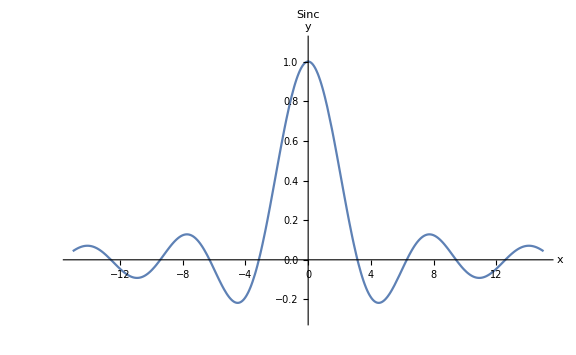

```mathematica
plotFun[Sinc[x],{{-15,15},{-.3,1.1}},{},"Sinc"]
```

# 2) Cos minus Cos

cos(x)-cos(y)=-2 sin((x+y)/2)sin((x-y)/2) ?

#### Useful formulas

Sin and Cos vs. Exp

cos(x)=(ⅇ^(ⅈ x)+ⅇ^(-ⅈ x))/2
sin(x)=(ⅇ^(ⅈ x)-ⅇ^(-ⅈ x))/(2ⅈ)

## Solution

cos(x)-cos(y)=(ⅇ^(ⅈ x)+ⅇ^(-ⅈ x))/2-(ⅇ^(ⅈ y)+ⅇ^(-ⅈ y))/2=1/2(ⅇ^(ⅈ x)-ⅇ^(-ⅈ y)+ⅇ^(-ⅈ x)-ⅇ^(ⅈ y))=1/2(ⅇ^(ⅈ (x-y)/2)(ⅇ^(ⅈ (x+y)/2)-ⅇ^(-ⅈ (x+y)/2))+ⅇ^(-ⅈ (x-y)/2)(ⅇ^(-ⅈ (x+y)/2)-ⅇ^(ⅈ (x+y)/2)))=1/2(2ⅈ ⅇ^(ⅈ (x-y)/2)((ⅇ^(ⅈ (x+y)/2)-ⅇ^(-ⅈ (x+y)/2))/(2ⅈ))-2ⅈ ⅇ^(-ⅈ (x-y)/2)((ⅇ^(-ⅈ (x+y)/2)-ⅇ^(ⅈ (x+y)/2))/(2ⅈ)))=ⅈ ⅇ^(ⅈ (x-y)/2)sin((x+y)/2)-ⅈ ⅇ^(-ⅈ (x-y)/2)sin((x+y)/2)=ⅈ sin((x+y)/2)((ⅇ^(ⅈ (x-y)/2)-ⅇ^(-ⅈ (x-y)/2))/(2ⅈ))2ⅈ=
-2 sin((x+y)/2)sin((x-y)/2)

# 3) Exp

f: ℝ→ℝ
f(x)=exp(x)

Stetig?

#### Useful formulas

ϵ-δ-Kriterium

f: D→ℝ stetig in x_0∈D, wenn (∀ϵ>0)( ∃δ>0)(∀x∈D):

Abs[x-x_0]<δ   ⇒  Abs[f(x)-f(x_0)]<ϵ

Restgliedabschätzung für die komplexe Exponentialfunktion

exp(x)=∑_(n=0)^N x^n/(n!)+R_(N+1)(x),

Abs[R_(N+1)(x)]≤2 Abs[x]^(N+1)/((N+1)!),  Abs[x]≤N/2+1

Product of exponentials

exp(x)=exp(x_0)·exp(x-x_0)

## Solution

## a) Stetig in x_0=0

ϵ-δ-Kriterium tells us we have to prove that:

Abs[x-0]<δ   ⇒  Abs[exp(x)-exp(0)]<ϵ

We can use the Restgliedabschätzung for N=2 to get:

Abs[exp(x)-exp(0)]=Abs[exp(x)-1]=Abs[(1+x+R_2(x))-1]=Abs[x+R_2(x)]

And so:

Abs[x+R_2(x)]≤Abs[x]+Abs[R_2(x)]≤Abs[x]+2 Abs[x]^2/(2!)=Abs[x]+Abs[x]^2<Abs[x]+Abs[x]=2Abs[x]

where the last inequality holds for Abs[x]<1. We may conclude that:

Abs[exp(x)-exp(0)]≤2Abs[x]

If for a given δ we define ϵ:=2δ, we get:

Abs[x]<δ   ⇒  Abs[exp(x)-exp(0)]≤2Abs[x]<ϵ

as we were to prove.

## b) Stetig in x_0≠0

|exp(x)-exp(x_0)|=|exp(x-x_0)·exp(x_0)-exp(x_0)|=Abs[exp(x_0)]·Abs[exp(x-x_0)-1]

But x_1:=x-x_0 tends to zero, so we can use the result for x_0=0 proven above to get:

Abs[exp(x_0)]·Abs[exp(x-x_0)-1]≤ Abs[exp(x_0)]·ϵ

As ϵ gets smaller, also  Abs[exp(x_0)]·ϵ gets smaller and therefore also Abs[exp(x)-exp(x_0)] tends to zero, as we wanted to show.

# 4) Rationale Funktion

f: ℝ\{-1}→ℝ
f(x)=1/(x+1)

lim_(x↘-1) f(x)=?
lim_(x↗-1) f(x)=?

#### Useful formulas

Limit of a function

f: D→ℝ;  D⊂ℝ;  x_0∈ℝ   Häufungspunkt

lim_(x→x_0) f(x)=y_0

∀(a_n)⊂D,a_n≠x_0, lim_(n→∞) a_n=x_0:  lim_(n→∞) f(a_n)=y_0

## Plot

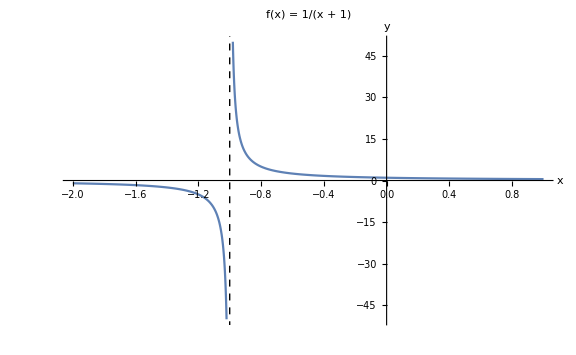

```mathematica
plotFun[1/(1+x),{{-2,1},{-50,50}},{Dashed,InfiniteLine[{-1,0},{0,1}]},"f(x) = 1/(x + 1)"]
```

## Solution

From the plot above we see that lim_(x↘-1) f(x) is very likely equal to +∞ and lim_(x↗-1) f(x) is very likely -∞. We have to check it now mathematically.

## a) lim_(x↘-1) f(x)

For lim_(x↘-1) f(x) we consider a Folge a_n, for which lim_(n→∞) a_n=-1 and a_n>-1. That is:

(∀ϵ>0)(∃N∈ℕ)(∀n∈ℕ, n>N)(Abs[a_n-(-1)]<ϵ)

Because a_n>-1 we have:

Abs[a_n-(-1)]=a_n-(-1)=a_n+1<ϵ   ⇒   1/ϵ<1/(a_n+1)

To show lim_(x↘-1) f(x)=∞ we need to prove that:

(∀K>0)(∃N∈ℕ)(∀n∈ℕ, n>N)(  f(a_n)>K  )

When we define K:=1/ϵ we get:

f(a_n)=1/(a_n+1)>1/ϵ=K

which completes the proof.

## b) lim_(x↗-1) f(x)

For lim_(x↗-1) f(x) we consider a Folge a_n, for which lim_(n→∞) a_n=-1 and a_n<-1. That is:

(∀ϵ>0)(∃N∈ℕ)(∀n∈ℕ, n>N)(Abs[a_n-(-1)]<ϵ)

Because a_n<-1 we have:

Abs[a_n-(-1)]=-(a_n-(-1))=-(a_n+1)<ϵ   ⇒   -1/ϵ>1/(a_n+1)

To show lim_(x↗-1) f(x)=-∞ we need to prove that:

(∀K>0)(∃N∈ℕ)(∀n∈ℕ, n>N)(  f(a_n)<-K  )

When we define K:=1/ϵ we get:

f(a_n)=1/(a_n+1)<-1/ϵ=-K

which completes the proof.

# 5) Landau

a) sin(x^2)=ℴ(x),  x→0

b) x/(√(x^2+1))=𝒪(1),  x→∞

c) lim_(x→1) (x^2+2x-3)/(x^2-1)=2 ?

#### Useful formulas

Landau symbol 𝒪

f(x)=𝒪(g(x)), x→∞

(∃δ>0, C>0)(∀x∈[δ, ∞))(  Abs[f(x)]≤CAbs[g(x)] )

Landau symbol ℴ

f(x)=ℴ(g(x)), x→a≠∞

(∀ϵ>0)(∃δ>0)(∀x∈(a-δ,a+δ))(Abs[f(x)]≤ϵ Abs[g(x)])

Limit of a function

f: D→ℝ;  D⊂ℝ;  x_0∈ℝ   Häufungspunkt

lim_(x→x_0) f(x)=y_0

∀(a_n)⊂D,a_n≠x_0, lim_(n→∞) a_n=x_0:  lim_(n→∞) f(a_n)=y_0

## Plots

## a)

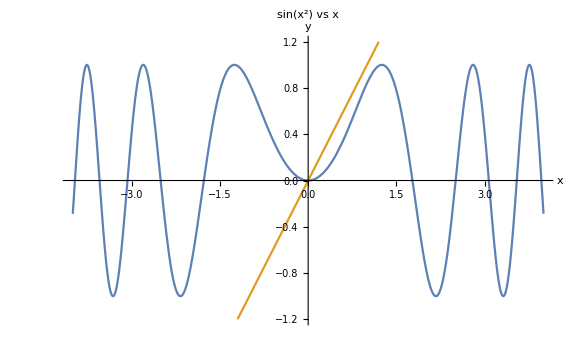

```mathematica
plotFun[{Sin[x^2],x},{{-4,4},{-1.2,1.2}},{},"sin(x^2) vs x"]
```

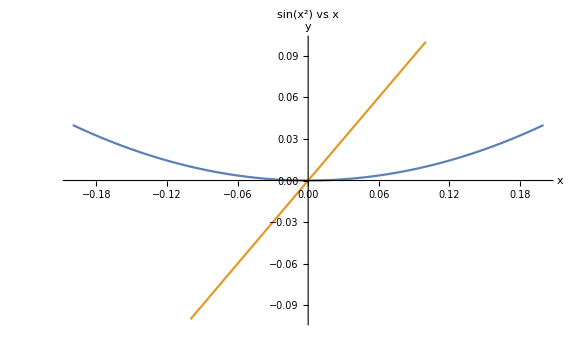

```mathematica
plotFun[{Sin[x^2],x},{{-.2,.2},{-.1,.1}},{},"sin(x^2) vs x"]
```

## b)

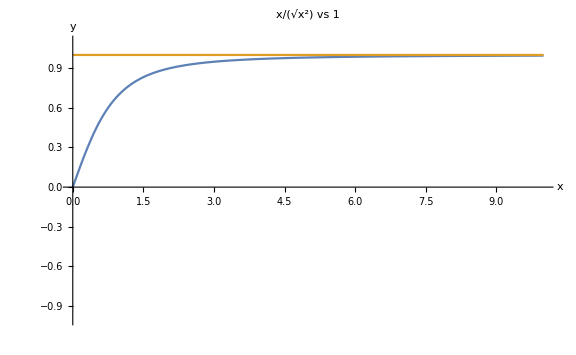

```mathematica
plotFun[{x/(√(x^2+1)),1},{{0,10},{-1,1.1}},{},"x/(√(x^2))   vs   1"]
```

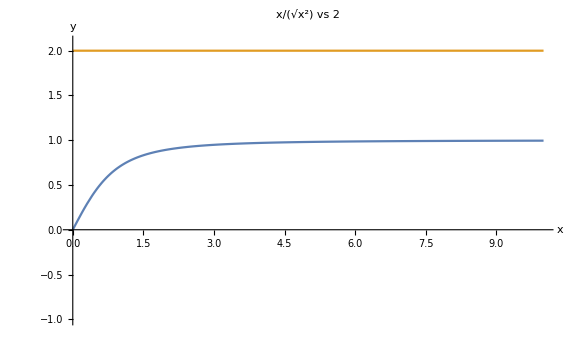

```mathematica
plotFun[{x/(√(x^2+1)),2},{{0,10},{-1,2.1}},{},"x/(√(x^2))   vs   2"]
```

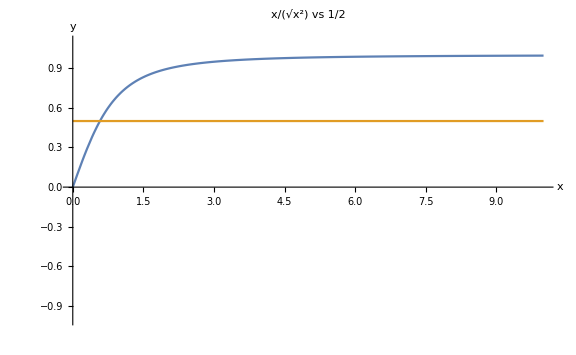

```mathematica
plotFun[{x/(√(x^2+1)),.5},{{0,10},{-1,1.1}},{},"x/(√(x^2))   vs   1/2"]
```

## c)

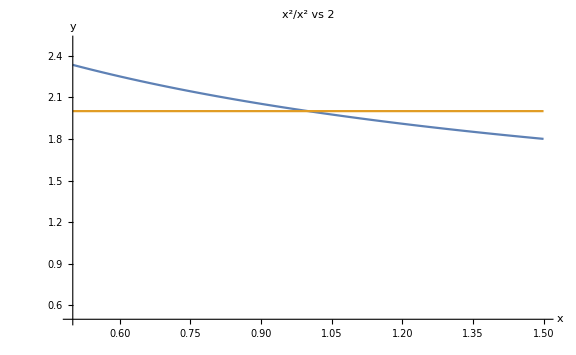

```mathematica
plotFun[{(x^2+2x-3)/(x^2-1),2},{{0.5,1.5},{.5,2.5}},{},"x^2/x^2   vs   2"]
```

## Solution

## a)

We have to check that:

(∀ϵ>0)(∃δ>0)(∀x∈(-δ,δ))(Abs[sin(x^2)]≤ϵ Abs[x])

Using Restgliedabschätzung for N=2 we get:

sin(x^2)=1/(2ⅈ)(ⅇ^(ⅈ x^2)-ⅇ^(-ⅈ x^2))=1/(2ⅈ)((1+ⅈ x^2+R_2(ⅈ x^2))-(1-ⅈ x^2+R_2(-ⅈ x^2)))=x^2+1/(2 ⅈ)(R_2(ⅈ x^2)-R_2(-ⅈ x^2))

For its absolute value then:

Abs[sin(x^2)]≤Abs[x]^2+1/2 Abs[R_2(ⅈ x^2)]+1/2 Abs[R_2(-ⅈ x^2)]≤Abs[x]^2+1/2(2 (Abs[ⅈ x^2]^2)/(2!)+2 (Abs[-ⅈ x^2]^2)/(2!))=Abs[x]^2+1/2(Abs[x]^4+Abs[x]^4)=Abs[x]^2+Abs[x]^4≤(2Abs[x])^2

where the last inequality holds for Abs[x]≤1. Since we consider only x in the range x∈(-δ,δ) it follows that Abs[x]<δ and thus:

Abs[sin(x^2)]≤(2Abs[x])^2=(2 Abs[x])·Abs[x]<(2 δ)·Abs[x]

When we define ϵ:=2 δ we finish the proof.

## b)

We have to check that:

(∃δ>0, C>0)(∀x∈[δ, ∞))(  Abs[x/(√(x^2+1))]≤C  )

If we choose δ:=0 and C:=1, we get:

Abs[x/(√(x^2+1))]≤1   ⇔  Abs[x]≤Abs[√(x^2+1)] ⇔  x^2≤x^2+1 ⇔ 0≤1

which is indeed true.

## c)

lim_(x→1) (x^2+2x-3)/(x^2-1)=lim_(x→1) ((x-1)(x+3))/((x-1)(x+1))=lim_(x→1) (x+3)/(x+1)

We could actually substitute for x in the above expression right away to get lim_(x→1) (x+3)/(x+1)=(1+3)/(1+1)=4/2=2 as there are no singularities that cause a problem, but let us calculate the limit properly.

Consider a Folge a_n with lim_(n→∞) a_n=1, that is:

(∀ϵ>0)(∃N∈ℕ)(∀n∈ℕ, n>N)(Abs[a_n-1]<ϵ)

From where it follows that for high n we have a_n>0 and:

Abs[a_n-1]<ϵ  ⇔ -ϵ<a_n-1<ϵ ⇔ 2-ϵ<a_n+1<2+ϵ

from where 2-ϵ<Abs[a_n+1]

We want to show that:

(∀ϵ>0)(∃N∈ℕ)(∀n∈ℕ, n>N)(Abs[f(a_n)-2]<ϵ)

where f(x):=(x+3)/(x+1). So:

Abs[f(a_n)-2]=Abs[(a_n+3)/(a_n+1)-2]=Abs[(a_n-1)/(a_n+1)]

When we use Abs[a_n-1]<ϵ and inequality 2-ϵ<Abs[a_n+1], we get:

Abs[(a_n-1)/(a_n+1)]<ϵ/Abs[a_n+1]<ϵ/(2-ϵ)≤ϵ/(2-1)=ϵ

for all ϵ≤1. In total, we showed Abs[f(a_n)-2]<ϵ for an arbitrary appropriate Folge a_n, as was to be done.